# Thesis Notebook

## 2D Orbit with the suns density profile and mass function, along with dissipative forces

## Setting functions up and choosing variables

```mathematica
(*R values in Schwarzschild coordinates*)
RStar = 8;(*Radius of the Star*)
M = 1;
```

## Exterior Schwarzschild Isotropic coordinates definitions r(r̄), r̄(r), A(r̄), α(r̄)

### r(r̄) and r̄(r) functions

```mathematica
rofrbarOutside[rbar_] :=rbar (1 + M/(2 rbar))^2; 

rbarofrOutside[r_] := 1/2 (-M + r + Sqrt[r^2 - 2 M r]);
```

### A(r̄), α(r̄)

```mathematica
A[rbar_] :=(1 + M/(2 rbar))^2;
α[rbar_] :=(1 - M/(2 rbar))/(1 + M/(2 rbar));
```

Getting the value of the radius of the star in isotropic coordinates

```mathematica
rbarStar = rbarofrOutside[RStar] //  N
```

6.9641

## TOV Isotropic coords definitions

### Mass and Density functions from 2405.08113

#### Fixing the rho0 by letting the total mass integral equal to 1

```mathematica
rho[r_] := rho0(1 - r/R)^6;
massIntegral =  4 Pi Integrate[rho[r] r^2, {r, 0, R}]; (*Set equal to 1*)
```

```mathematica
rhoCentre[R_] := 63/(Pi R^3) (*From the above*)
rho0 = rhoCentre[RStar];
```

```mathematica
MassFunc[r_] := Piecewise[{{252(r^9/(9 RStar^9)-(3 r^8)/(4 RStar^8)+(15 r^7)/(7 RStar^7)-(10 r^6)/(3 RStar^6)+(3 r^5)/RStar^5-(3 r^4)/(2 RStar^4)+r^3/(3 RStar^3)) , r < RStar},
{M, r >= RStar}
}];
(*In 2405.08113 this function is divided by the solar mass, here I use M=1*)
```

### New density function

```mathematica
rho[r_] := Piecewise[{
{rho0(1 - r/RStar)^6, r < RStar},
{0, r >= RStar}
}];
```

### Getting new equations for the new interior metric:

```mathematica
(*TOV differential equation*)
(*dPdr[r_, Pressure_] := -Simplify[MassFunc[r]/r^2(rho[r] + Pressure)(1 + (4 Pi (Pressure) r^3)/MassFunc[r])(1 - (2 MassFunc[r])/r)^-1];*)
dPdr[r_, Pressure_] := Simplify[-(rho[r] + Pressure)((MassFunc[r] + 4 Pi Pressure r^3)/(r(r-2MassFunc[r])))];
```

```mathematica
(*Phi differential equation for metric*)
dPhidrMetric[r_, Pressure_] := Simplify[((MassFunc[r] + 4 Pi Pressure r^3)/(r(r-2MassFunc[r])))];
```

#### Numerically Integrate these two partially coupled differential equations

```mathematica
rmin = 10^-16 (*For these integrations*);
```

```mathematica
eq1 = P'[r] == dPdr[r, P[r]];
eq2 = Phi'[r] == dPhidrMetric[r, P[r]];
BCs = {P[RStar] == 0, Phi[RStar] == 1/2 Log[1-2 M/RStar]} ;(*Phi[RStar] from the Schwarzschild metric*)
```

```mathematica
sol1 = NDSolve[
{eq1,
eq2,
BCs},
{P, Phi},
{r, RStar, rmin}
][[1]]; (*Very small rmin to avoid singularity sarp mentioned*)
```

```mathematica
(*Maybe extrapolated points after the region of interest I solved is causing problems?*)
```

```mathematica
(*Pressure[r_?NumericQ] = Piecewise[
{
{P[r] /. sol1, r <RStar},
{0, r >= RStar}
}
];*)

Pressure[r_] := P[r] /. sol1

PhiMetric[r_?NumericQ] = Phi[r] /. sol1;

(*Plot[Derivative[1][PhiMetric][r], {r, 0, RStar}]*)
(*Causing the issue it seems, but we have this Analytically!*)
```

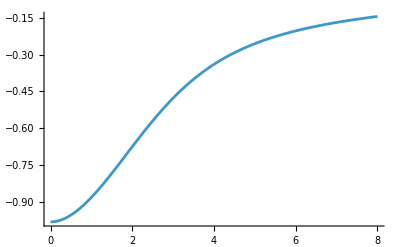

```mathematica
Plot[PhiMetric[r], {r, 0, RStar}]
```

#### Solving for the new r̄(r) and r(r̄) inside, obtaining r(r̄) via the interpolation trick Sarp explained

```mathematica
(*Defining the ODE*)
drbardr[rbar_, r_] := rbar/r(1 - (2MassFunc[r])/r)^(-1/2)
```

Numerically Integrating the above equation.

```mathematica
eq = rbarofr'[r] == drbardr[rbarofr[r], r];
BC = {rbarofr[RStar] == rbarStar};
```

```mathematica
sol2 = NDSolve[
{eq,
BC},
{rbarofr},
{r, RStar, rmin}
][[1]];
```

```mathematica
rbarofrInside[r_] = rbarofr[r] /. sol2;
```

```mathematica
rbarofrInside[RStar]
rbarofrOutside[RStar] //N
```

6.9641

6.9641

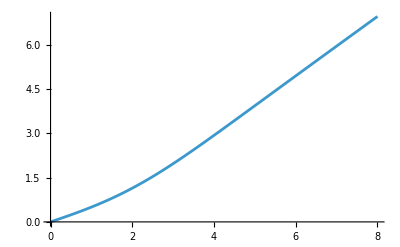

```mathematica
Plot[rbarofrInside[r], {r, 0, RStar}]
```

Now using the interpolation trick to obtain r(r̄):

```mathematica
(*Generating the numerical data points:*)
(*Table[ expression, {variable, start, end, step}*)
data = Prepend[Table[
{rbarofrInside[r], r}, (*Here Mathematica stores rbar[r] and r as a 2 element list - first entry is the independent variable and the one after is the dependent variable*)
{r, rmin, RStar, (RStar - rmin)/100000} (*500 points*)
], {0,0}];
```

```mathematica
(*Evaluates ok at zero as sapr mentioned but integral doesn't like it one bit*)
```

```mathematica
(*Inverse Interpolation*)
rofrbarInside = Interpolation[data];(*Builds a function from the data passing through all points unlike Fit which approximately matches the data to a function I give it with parameters,  FindFit finds the parameters for me given I guess a suitable function*)
```

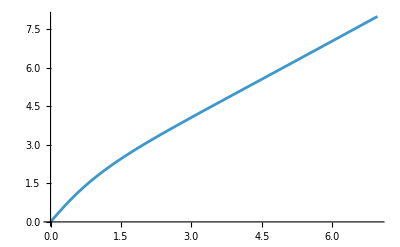

```mathematica
Plot[rofrbarInside[rbar], {rbar, 0, rbarStar}]
```

```mathematica
rofrbarInside[0]
```

0.

#### Writing clean full r(r̄) equation to try and rid discontinuities

```mathematica
rofrbarFull[rbar_?NumericQ] := Piecewise[
{
{rofrbarInside[rbar], rbar < rbarStar},
{rofrbarOutside[rbar], rbar >= rbarStar}
}
];
```

### Putting this together to find the new interior metric functions

#### finding alpha in terms of normal r first

```mathematica
dPhidrMetric[r_] := ((MassFunc[r] + 4 Pi Pressure[r] r^3)/(r(r-2MassFunc[r])))
```

```mathematica
alpha[r_] := Exp[PhiMetric[r]]
DERalphaIns[r_] := dPhidrMetric[r] alpha[r]
```

Exterior alpha derivative

```mathematica
DERαOutsiderbardummy = Derivative[1][α][rbar];
DERαOutsiderbar[r_] := ((1-1/(2 rbar))/(2 (1+1/(2 rbar))^2 rbar^2)+1/(2 (1+1/(2 rbar)) rbar^2) )/. rbar -> rbarofrOutside[r] (*More accurate subbing in after for rbar maybe?*)
drbardr[r_] := rbarofrOutside[r]/r(1 - (2MassFunc[r])/r)^(-1/2)
```

```mathematica
DERalpha[r_] := drbardr[r]  DERαOutsiderbar[r]
```

```mathematica
DERalpha[RStar] //N
DERalphaIns[RStar] //N
```

0.0180422

0.0180422

```mathematica
DERalpha[rbarofrOutside[RStar]] //N
DERalphaIns[rbarofrInside[RStar]] //N
```

0.024422

0.0244215

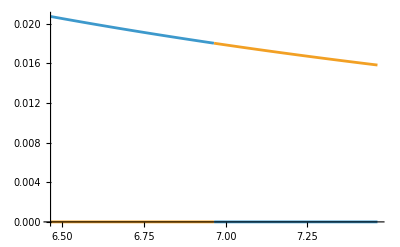

```mathematica
Plot[{Piecewise[{{DERalphaIns[rofrbarInside[rbar]],rbar<=rbarStar}}],Piecewise[{{DERalpha[rofrbarOutside[rbar]],rbar>=rbarStar}}]},{rbar,rbarStar-0.5,rbarStar+0.5}]
```

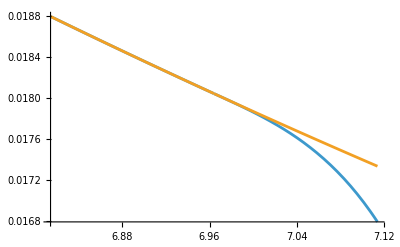

```mathematica
Plot[{DERalphaIns[rofrbarInside[rbar]],DERalpha[rofrbarOutside[rbar]]},{rbar,rbarStar-0.15,rbarStar+0.15}]
```

```mathematica
DERαOutside[rbar_] := drbardr[rofrbarOutside[rbar]]  DERαOutsiderbar[rofrbarOutside[rbar]]
DERαInside[rbar_] := dPhidrMetric[rofrbarInside[rbar]] alpha[rofrbarInside[rbar]]
```

```mathematica
DERαFull[rbar_] := Piecewise[
{
{DERαInside[rbar], rbar < rbarStar},
{DERαOutside[rbar], rbar >= rbarStar}
}
]
```

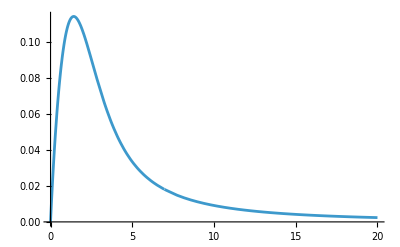

```mathematica
Plot[DERαFull[rbar], {rbar, 0, 20}]
```

```mathematica
αInside[rbar_?NumericQ] := Exp[PhiMetric[rofrbarInside[rbar]]]
```

```mathematica
αInside[rbarStar]
α[rbarStar]
```

0.866025

0.866025

```mathematica
αFull[rbar_] := Piecewise[
{
{αInside[rbar], rbar < rbarStar},
{α[rbar], rbar >= rbarStar}
}
]
```

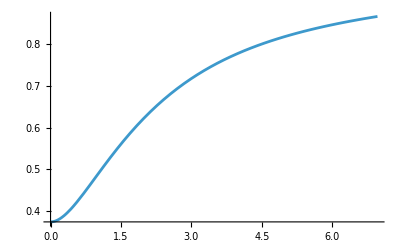

```mathematica
Plot[αFull[rbar], {rbar, 0, rbarStar}]
```

```mathematica
(*Plot[Derivative[1][αFull][rbar], {rbar, 0.4, rbarStar}]*) (*Phi metric causing the issue as it's the numerically integrating thing we are differentiating*)
```

Going to do the same derivative setup as the α component for the A component

```mathematica
AInside[rbar_?NumericQ] := rofrbarInside[rbar]/rbar;
```

```mathematica
A[rbarStar]
AInside[rbarStar]
```

1.14875

1.14875

```mathematica
AFull[rbar_] := Piecewise[
{
{A[rbar], rbar >= rbarStar},
{AInside[rbar], rbar < rbarStar}
}
];
```

```mathematica
drbardr[rbar_, r_] := rbar/r(1 - (2MassFunc[r])/r)^(-1/2)
drdrbar[rbar_] := rofrbarInside[rbar]/rbar(1 - (2MassFunc[rofrbarInside[rbar]])/rofrbarInside[rbar])^(1/2)
```

```mathematica
DERAInside[rbar_] := drdrbar[rbar]/rbar - rofrbarInside[rbar]/rbar^2;
DERAOutside[rbar_] := Derivative[1][A][rbar]
```

```mathematica
DERAFull[rbar_] := Piecewise[
{
{DERAOutside[rbar], rbar >=rbarStar},
{DERAInside[rbar], rbar < rbarStar}
}
];
```

```mathematica
DERAOutside[rbarStar]
DERAInside[rbarStar]
```

-0.0220995

-0.0220995

### Sorting out the speed of sound as a function of r: a(r)

```mathematica
(*Getting the derivative of the density*)
rhodummy[r_] := rho0(1 - r/RStar)^6

drhodr[r_] := rhodummy'[r]
```

```mathematica
asos[r_] := (dPdr[r, Pressure[r]]/drhodr[r])^(1/2);
```

```mathematica
asos[10^-12]; (*zero does not work but small r does!*)
```

```mathematica
asos[RStar*.99989789203]
(*turns out to be nice cut off for the asos variable, could use this?*)
```

0.00168436

```mathematica
RStar*.99989789203
```

7.99918

```mathematica
cutoffRStar = RStar*.99989789203;
cutoffRStar1 = RStar*.999
```

7.992

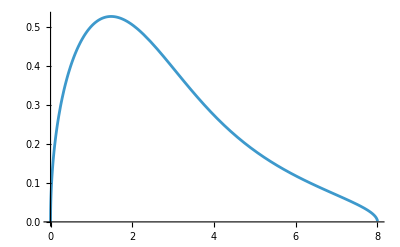

```mathematica
Plot[asos[r], {r, 0, cutoffRStar}]
```

#### Gets very messy from here downwards: doing it the Taylor expansion way

Limit at RStar diverges -> Taylor expland

```mathematica
Pdoubleprime[r_] := D[dPdr[x, Pressure[x]], x] /. x->r  (*Must use D as ' only differentiates wrt. the first argument*)
```

```mathematica
asosprimenearRStar[r_] := 1/(2 √asos[r])(Pdoubleprime[r]/drhodr[r] - dPdr[r, Pressure[r]]/(drhodr[r])^2 drhodr'[r])
asosprimenearRStar[7.974] // N;
```

```mathematica
epsilon = 0.026; (*from RStar - 7.974 which is oscillating only in the 1e-4 range for alphaprime which is very small*)
```

```mathematica
asosprimenearRStar[7.974]*epsilon (*could either use this?*)
```

-0.000468246

Attempting to double differentiate and see where the function hits zero to find the max and minimum value of a’ in order to find the value of r to make a(r) a minimum

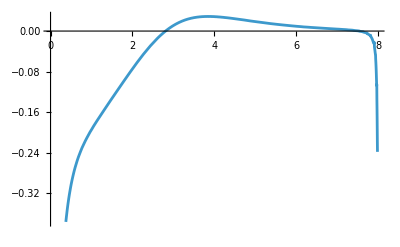

```mathematica
Plot[asosprimenearRStar'[r], {r, 0, 7.984}]
```

```mathematica
func[r_] := Pdoubleprime[r]/drhodr[r] - dPdr[r, Pressure[r]]/(drhodr[r])^2 drhodr'[r]
func[.999*RStar];
```

```mathematica
Pdoubleprime[RStar*.999]/drhodr[RStar*.999];
```

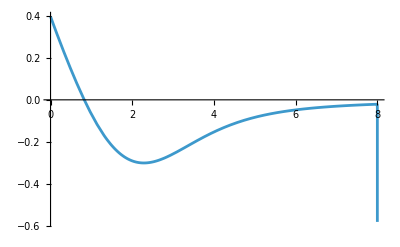

```mathematica
Plot[Pdoubleprime[r]/drhodr[r], {r, 0, RStar}]
```

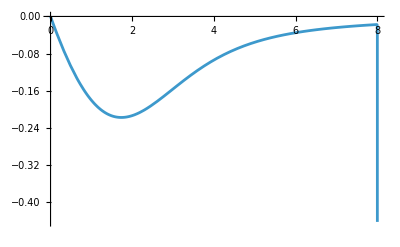

```mathematica
Plot[dPdr[r, Pressure[r]]/(drhodr[r])^2 drhodr'[r], {r, 0, RStar}]
```

#### Speed of sound in isotropic coordinates

```mathematica
cutoffrbarStar = rbarofrInside[cutoffRStar];
rbarStar;
Abs[cutoffrbarStar-rbarStar](*Very close*)
```

0.000821097

```mathematica
asosPiecewise[rbar_?NumericQ] := Piecewise[
{
{asos[rofrbarInside[rbar]], rbar < cutoffrbarStar},
{asos[rofrbarInside[cutoffrbarStar]], rbar >= cutoffrbarStar}
}
];
```

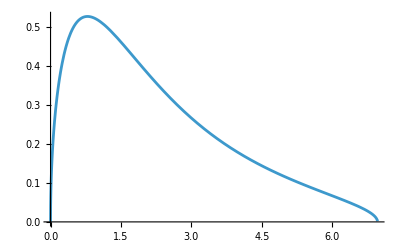

0.00168436

```mathematica
Plot[asosPiecewise[rbar], {rbar, 0, rbarStar}]
asosPiecewise[rbarStar]
```

#### Density and Pressure in isotropic coordinates

```mathematica
rho0 = rhoCentre[RStar];
```

```mathematica
rho[rbar_?NumericQ] :=Piecewise[
{
{rho0(1 - rofrbarInside[rbar]/RStar)^6, rbar < rbarStar},
{0, rbar >= rbarStar}
}
];

IsotropicCoordsPressure[rbar_?NumericQ] := Piecewise[
{
{Pressure[rofrbarInside[rbar]], rbar < rbarStar},
{0, rbar >= rbarStar}
}
]; (*Defined above*)

IsotropicCoordsPressure[0];
```

## Setting up 2D ODEs for new density profile:

Constants that are going to be used

```mathematica
m = 10^-6; (*mass of PBH?*)
λGR[rbar_] := 1.49*asosPiecewise[rbar]
q = 2;
(*η = 3.25 10^4) (*72.5 nice from prev sims*)(*10^5 - it dives; 10^4 it orbits*)
```

32500.

### Mach number interpolation

#### Interpolating

```mathematica
x1 = 1;
x2 = 1;
y1 = 3.03;
y2 = 6.67;

anaylticline[Μach_] := y1 + (y2 - y1) (x - x1)/(x2 - x1);
```

```mathematica
IVariableInterpolated[Μach_] := Piecewise[{
{1/2 Log[(1+ Μach)/(1 - Μach)] - Μach, Μach < 0.9999},
{anaylticline[Μach], 0.9999 < Μach  < 1.0001},
{1/2 Log[1 - 1/Μach^2]  + 10, Μach > 1.0001}
}];
```

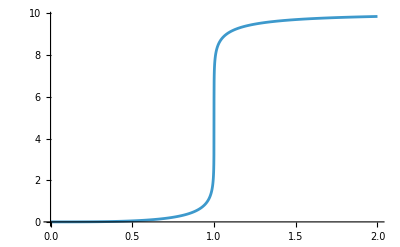

```mathematica
Plot[IVariableInterpolated[Mach], {Mach, 0, 2}, PlotRange->All, Exclusions->None]
```

### Outside Star

#### Velocities

```mathematica
Ut[rbar_, ur_, uphi_] := (√(1 + (ur/A[rbar])^2 + (uphi/(rbar A[rbar]))^2))/α[rbar];
```

#### Rates of change of velocities

```mathematica
drBardt[rbar_, ur_, uphi_] := 1/(A[rbar]^2 Ut[rbar, ur, uphi])ur;

dphidtOutside[rbar_,ur_, uphi_] := 1/(rbar^2*A[rbar]^2*Ut[rbar, ur,uphi])uphi;

durdt2DOutside[rbar_, ur_, uphi_] := -α[rbar] Ut[rbar, ur, uphi] DERαOutside[rbar] + ur^2/Ut[rbar, ur, uphi](DERAOutside[rbar]/A[rbar]^3) + uphi^2/Ut[rbar, ur, uphi](1/(rbar^3 *A[rbar]^2) + DERAOutside[rbar]/(rbar^2*A[rbar]^3));
```

### Inside Star

#### Velocities

```mathematica
UtInside[rbar_, ur_, uphi_] := (√(1 + (ur/AFull[rbar])^2 + (uphi/(rbar AFull[rbar]))^2))/αFull[rbar];
umagphi[rbar_, ur_, uphi_] := Piecewise[
{
{(√(ur^2+(uphi/rbar)^2))/AFull[rbar], rbar <rbarStar},
{(√(ur^2+(uphi/rbar)^2))/A[rbar], rbar >= rbarStar}
}
];(*paper eqn ut and umagphi*)
```

#### Mach business

```mathematica
Mach[rbar_, ur_, uphi_] := Piecewise[
{
{umagphi[rbar, ur, uphi]/(asosPiecewise[rbar]  α[rbar] Ut[rbar, ur, uphi]), rbar >= rbarStar},
{umagphi[rbar, ur, uphi]/(asosPiecewise[rbar] αFull[rbar] UtInside[rbar, ur, uphi]), rbar < rbarStar}
}
];
```

#### Dissipative Forces

Accretion

```mathematica
(* for Γ = 2 accretion rate*) (*This is my dmdt equation*)

(*mdot[m_, rbar_, ur_, uphi_] := 1.49* (4Pi rho0 m^2)/(asosPiecewise[rbar]^2 + (umagphi[rbar, ur, uphi]/(αFull[rbar] UtInside[rbar, ur, uphi]))^2);
(*dpdtaccretionr[m_, rbar_, ur_, uphi_] := -((4 Pi αFull[rbar] λGR[rbar](rho[rbar] + IsotropicCoordsPressure[rbar])m^2)/asosPiecewise[rbar]^3)(asosPiecewise[rbar]^2/(asosPiecewise[rbar]^2+(umagphi[rbar, ur, uphi]/(αFull[rbar] UtInside[rbar, ur, uphi]))^2))^(q/2)ur;

dpdtaccretionphi[m_, rbar_, ur_, uphi_] := -((4 Pi αFull[rbar] λGR[rbar](rho[rbar] + IsotropicCoordsPressure[rbar])m^2)/asosPiecewise[rbar]^3)(asosPiecewise[rbar]^2/(asosPiecewise[rbar]^2+(umagphi[rbar, ur, uphi]/(αFull[rbar] UtInside[rbar, ur, uphi]))^2))^(q/2)uphi*)
```

```mathematica
(*dpdtaccretionr[m_, rbar_, ur_, uphi_] := -((4 Pi αFull[rbar] (1.49)(rho[rbar] + IsotropicCoordsPressure[rbar])m^2))(1/(asosPiecewise[rbar]^2+(umagphi[rbar, ur, uphi]/(αFull[rbar] UtInside[rbar, ur, uphi]))^2))^(q/2)ur;
(*Removing the a here as it cancels in this regime with q=2 and Γ = 2*)
dpdtaccretionphi[m_, rbar_, ur_, uphi_] := -((4 Pi αFull[rbar] (1.49)(rho[rbar] + IsotropicCoordsPressure[rbar])m^2))(1/(asosPiecewise[rbar]^2+(umagphi[rbar, ur, uphi]/(αFull[rbar] UtInside[rbar, ur, uphi]))^2))^(q/2)uphi*)
```

Drag

```mathematica
dpdtdragphi[rbar_, ur_, uphi_] := 1/umagphi[rbar, ur, uphi]^3(-4π αFull[rbar]*(rho[rbar] + IsotropicCoordsPressure[rbar])*m^2*(1 + 2 umagphi[rbar, ur, uphi]^2)^2 *IVariableInterpolated[Mach[rbar, ur, uphi]] *uphi);

dpdtdragr[rbar_, ur_, uphi_] := (-4π αFull[rbar](rho[rbar] + IsotropicCoordsPressure[rbar])m^2(1 + 2 umagphi[rbar, ur, uphi]^2)^2 IVariableInterpolated[Mach[rbar, ur, uphi]] *ur)/umagphi[rbar, ur, uphi]^3;
```

#### Rates of change of velocities

```mathematica
drBardtInside[rbar_, ur_, uphi_] := 1/(AFull[rbar]^2 UtInside[rbar, ur, uphi])ur;

dphidtInside[rbar_, ur_, uphi_] := 1/(rbar^2 AFull[rbar]^2 UtInside[rbar, ur, uphi])uphi;

duphidtInside[rbar_, ur_, uphi_] := 0;

durdt2DInside[rbar_, ur_, uphi_] := -αFull[rbar] UtInside[rbar, ur, uphi] DERαFull[rbar] + ur^2/UtInside[rbar, ur, uphi](DERAFull[rbar]/AFull[rbar]^3) + uphi^2/UtInside[rbar, ur, uphi](1/(rbar^3 AFull[rbar]^2) + DERAFull[rbar]/(rbar^2 AFull[rbar]^3)) ;
```

## Defining Energy and Angular momentum per unit mass functions along with other orbital parameters

```mathematica
EnergyPerUnitMass[ptilde_, eccen_] := √(((ptilde -2)^2 - 4 *eccen^2)/(ptilde*(ptilde - 3 - eccen^2)));
LPerUnitMass[ptilde_, M_, eccen_] := (ptilde*M)/(√(ptilde - 3 - eccen^2));
ptildefunc[p_, Mass_] := p/Mass;
rapoapsis[eccen_, ptilde_, Mass_] := ((ptilde)*Mass)/(1 - eccen); (*In Schwarzschild areal r coordinates*)
rperiapsis[eccen_, ptilde_] := ptilde/(1+eccen);
```

### Defining the constants to define the motion

#### Eccentricity and semi-latus rectum

```mathematica
eccentricity = 0.4;
semilatrecP = 10;
ptilde = ptildefunc[semilatrecP, M];
```

#### Energy and Angular momentum per unit mass

```mathematica
Energy = EnergyPerUnitMass[ptilde, eccentricity];
AngularMomentumUphi0 = LPerUnitMass[ptilde, M, eccentricity];
```

Initial drop radius (apoapsis), closest point it goes to (perihelion), defining Isotropic star radius

```mathematica
r0 = rapoapsis[eccentricity, ptilde, M];
rbar0 = rbarofrOutside[r0];
```

#### Must satisfy this inequality to pass through star

```mathematica
ptilde < RStar(1+eccentricity)
ptilde > 6 + 2eccentricity
```

True

True

## Solving the ODEs

```mathematica
drBardtInside[rbarStar,0, AngularMomentumUphi0]
durdt2DInside[rbarStar,0, AngularMomentumUphi0]
duphidtInside[rbarStar,0, AngularMomentumUphi0]
dphidtInside[rbarStar,0, AngularMomentumUphi0]
```

0.

0.00219943

0

0.0466817

```mathematica
t0=0;
tEnd=6000;
η = 32500;

solIn=NDSolve[
{
rbar'[t]==
Piecewise[
{
{drBardt[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{drBardtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
ur'[t]==
Piecewise[
{
{durdt2DOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{durdt2DInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
uphi'[t]==
Piecewise[
{
{0,rbar[t]>=rbarStar},
{duphidtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
phi'[t]==
Piecewise[
{
{dphidtOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{dphidtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
rbar[0]== rbar0,
ur[0]==0,
phi[0]==0,
uphi[0]==AngularMomentumUphi0,

WhenEvent[rbar[t] <= 10^-3 , "StopIntegration"]
},
{rbar,ur,phi,uphi},
{t,t0,tEnd},
MaxSteps->20000
][[1]];
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::smpf: Failure to project onto the discontinuity surface when computing Filippov continuation at time 5577.07.

```mathematica
rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
phiNumIn = phi /. solIn;
uphiNumIn = uphi /. solIn;
(*massNumIn = mass /. solIn;*)
```

```mathematica
tFinish = rbarNumIn["Domain"][[1,2]]
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}]
```

5577.07

159.895

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

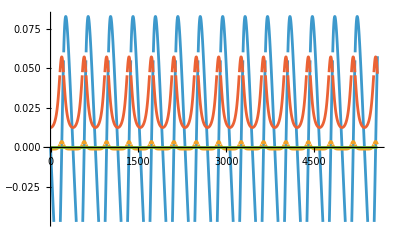

```mathematica
Plot[{drBardtInside[rbarNumIn[t],urNumIn[t], uphiNumIn[t]],
durdt2DInside[rbarNumIn[t],urNumIn[t], uphiNumIn[t]],
duphidtInside[rbarNumIn[t],urNumIn[t], uphiNumIn[t]],
dphidtInside[rbarNumIn[t],urNumIn[t], uphiNumIn[t]]}, {t, 0, tFinish}]
```

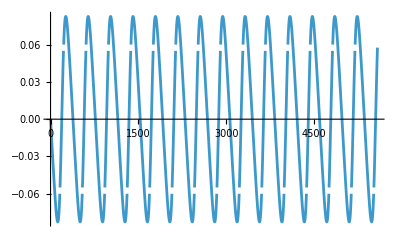

```mathematica
Plot[{drBardtInside[rbarNumIn[t],urNumIn[t], uphiNumIn[t]]}, {t, 0, tFinish}]
```

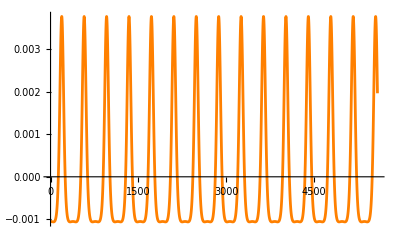

```mathematica
Plot[{durdt2DInside[rbarNumIn[t],urNumIn[t], uphiNumIn[t]]}, {t, 0, tFinish}, PlotStyle->Orange, PlotRange->All, Exclusions->None]
```

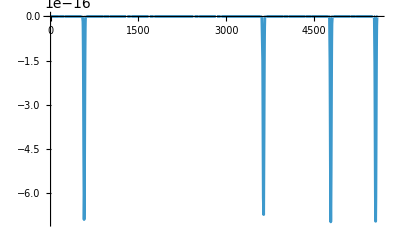

```mathematica
Plot[dpdtdragphi[rbarNumIn[t],urNumIn[t], uphiNumIn[t]], {t, 0, tFinish}]
```

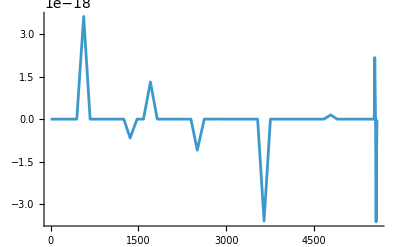

```mathematica
Plot[dpdtdragr[rbarNumIn[t],urNumIn[t], uphiNumIn[t]], {t, 0, tFinish}, Exclusions->None]
```

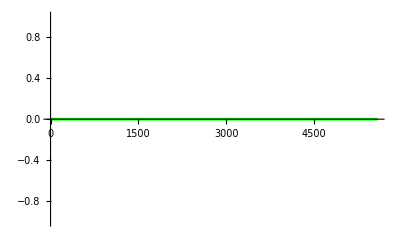

```mathematica
Plot[{duphidtInside[rbarNumIn[t],urNumIn[t], uphiNumIn[t]]}, {t, 0, tFinish}, PlotStyle->Green, Exclusions->None]
```

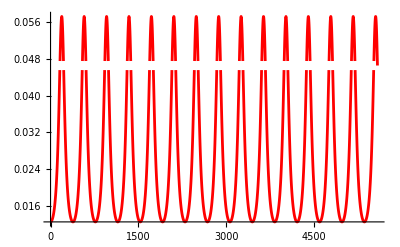

```mathematica
Plot[{dphidtInside[rbarNumIn[t],urNumIn[t], uphiNumIn[t]]}, {t, 0, tFinish}, PlotStyle->Red]
```

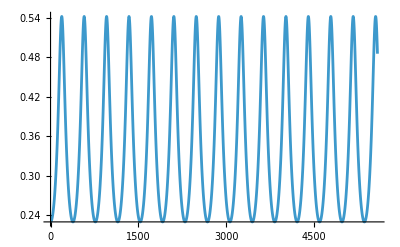

```mathematica
Plot[umagphi[rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 0, tFinish}, Exclusions->None] (*Normal behaviour judging from rho=const simulation*)
```

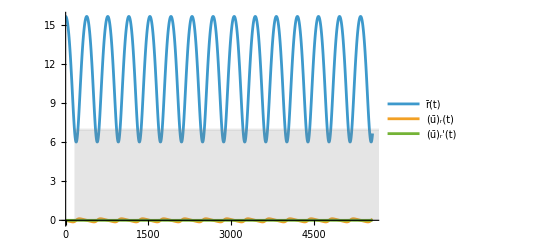

```mathematica
outFigRadial=Show[Plot[{rbarNumIn[t],urNumIn[t],urNumIn'[t]},{t,t0,.999 tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

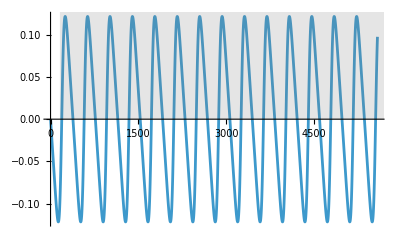

```mathematica
outFigRadial=Show[Plot[{urNumIn[t]},{t,t0, tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

```mathematica
outFigAngular=Plot[{uphiNumIn[t]},{t,t0,tFinish},PlotLegends->LineLegend[Automatic,{"phi(t)","uphi(t)","uphi'(t)"}]]
```

-Graphics-

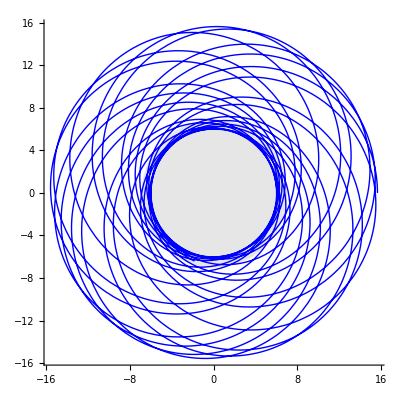

```mathematica
x[t_]:=rbarNumIn[t] Cos[phiNumIn[t]];
y[t_]:=rbarNumIn[t] Sin[phiNumIn[t]];
orbit2D=ParametricPlot[{x[t],y[t]},{t,t0,0.999 tFinish},AspectRatio->Automatic,AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Thick,Blue}];
(*Automatic scale makes the aces the same scale*)
centralBody=Graphics[{GrayLevel[0.9],Disk[{0,0},rbarStar]}];
Show[centralBody, orbit2D,AspectRatio->Automatic,PlotRange->All, Axes -> True]
```

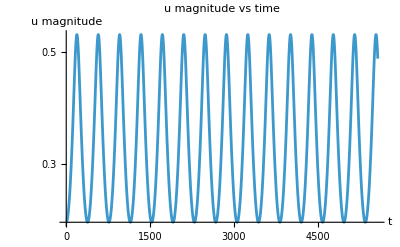

```mathematica
LogPlot[Evaluate[umagphi[rbarNumIn[t],urNumIn[t],uphiNumIn[t]]/. solIn],{t,0,tFinish},PlotRange->All,AxesLabel->{"t","u magnitude"},PlotLabel->"u magnitude vs time"]
(*Show me the value of u at tfinish*)
umagphi[rbarNumIn[tFinish],urNumIn[tFinish],uphiNumIn[tFinish]]/. solIn;
```